```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/deq_3loop_bubble_bubble

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Reverse[{1,1,1,1,1,0,0,0,0}]
FromDigits[%,2]
```

{0,0,0,0,1,1,1,1,1}

31

### Preliminaries: start basis

```mathematica
family = topoA;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
(*intfam  = {-m2+sp[k1,k1],-m2+sp[k2,k2],-m2+sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],-m2+sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k2]+sp[k2,k2],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3],sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]}*)
```

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2,k3},Directory->"famA"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];*)

(*Save to disk*)
(*DiskSave[family];*)
```

```mathematica
(*Get["./famA/famA"];*)
```

```mathematica
(*MIs[family]*)
```

```mathematica
(*MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];*)
```

```mathematica
(*LiteRed Masters*)
(*todiff= MIs[family];*)
```

```mathematica
(*(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;*)
```

### Start From d = 2

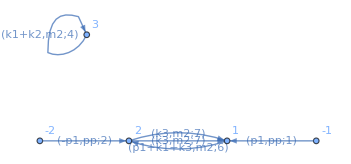

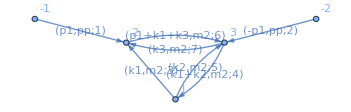

```mathematica
Import["./graphs/all/topoA_3_011.dot"]; (* triple tadpole*)
Import["./graphs/all/topoA_4_015.dot"];(*tadpole * tadpole2loop *)
Import["./graphs/all/topoA_4_027.dot"] (*tadpole * sunrise 2 loop, elliptic, 2 masters *)
Import["./graphs/all/topoA_4_030.dot"]; (* 3 loop banana, K3, 3 masters *)
Import["./graphs/all/topoA_5_031.dot"]  (* top sector, elliptic 3 masters *)
```

```mathematica
Reverse[IntegerDigits[11,2]]
Reverse[IntegerDigits[15,2]]
Reverse[IntegerDigits[27,2]]
Reverse[IntegerDigits[30,2]]
```

{1,1,0,1}

{1,1,1,1}

{1,1,0,1,1}

{0,1,1,1,1}

```mathematica
mybasis = {
topoA[1,1,0,1,0,0,0,0,0], (* 11 *)
topoA[1,1,1,1,0,0,0,0,0], (* 15 *)
topoA[1,1,0,1,1,0,0,0,0], (* 27: need to go to derivative basis*)
topoA[2,1,0,1,1,0,0,0,0], (* 27 *)
topoA[0,1,1,1,1,0,0,0,0], (* 30, K3 banana *)
topoA[0,2,1,1,1,0,0,0,0], (* 30 *)
topoA[0,1,1,2,2,0,0,0,0], (* 30 *)
topoA[1,1,1,1,1,0,0,0,0], (* 31 *)
topoA[1,1,1,2,2,0,0,0,0],(* 31 *)
(*topoA[2,1,1,1,1,0,0,0,0](* 31 *)*)
topoA[1,1,1,1,1,0,0,0,-1]
}
```

{topoA[1,1,0,1,0,0,0,0,0],topoA[1,1,1,1,0,0,0,0,0],topoA[1,1,0,1,1,0,0,0,0],topoA[2,1,0,1,1,0,0,0,0],topoA[0,1,1,1,1,0,0,0,0],topoA[0,2,1,1,1,0,0,0,0],topoA[0,1,1,2,2,0,0,0,0],topoA[1,1,1,1,1,0,0,0,0],topoA[1,1,1,2,2,0,0,0,0],topoA[1,1,1,1,1,0,0,0,-1]}

```mathematica
deq=Import["./deq.m"] /. INT["topoA",a__,{bin__}]:> topoA[bin];
```

```mathematica
derivative=mybasis /. topoA[a__]:> der[topoA[a],pp] /. deq /. m2 -> 1;
```

```mathematica
toreduce=Join[Union@Cases[derivative, _topoA, ∞],Union@Cases[mybasis 2, _topoA, ∞]]//Union
Do[
WriteLine["./to_reduce.inc",toreduce[[i]]], {i,1,Length[toreduce]}
]
```

{topoA[0,1,1,1,1,0,0,0,0],topoA[0,1,1,2,2,0,0,0,0],topoA[0,2,1,1,1,0,0,0,0],topoA[1,1,0,1,0,0,0,0,0],topoA[1,1,0,1,1,0,0,0,0],topoA[1,1,1,1,0,0,0,0,0],topoA[1,1,1,1,1,0,0,0,-1],topoA[1,1,1,1,1,0,0,0,0],topoA[1,1,1,2,2,0,0,0,0],topoA[2,1,0,1,1,0,0,0,0],topoA[2,1,1,1,1,0,0,0,0]}

```mathematica
reddeqlaporta=Import["./reduction.m"]/. INT["topoA",a__,{bin__}]:> topoA[bin];
```

```mathematica
reduzeLaporta = Union@Cases[mybasis /. reddeqlaporta, _topoA, ∞];
```

```mathematica
T=CoefficientArrays[mybasis /. reddeqlaporta/.m2-> 1, reduzeLaporta][[2]]//Normal//FullSimplify;
matMM=CoefficientArrays[Collect[derivative /. reddeqlaporta /. m2-> 1, {_topoA},Together],reduzeLaporta][[2]]//Normal;
```

```mathematica
(*Union@Cases[derivative /. reddeqlaporta /. m2-> 1// Together, _topoA, ∞]
Join[Union@Cases[ mybasis /. reddeqlaporta//Together, _topoA, ∞],Union@Cases[ reddeqlaporta[[;;,2]]// Together, _topoA, ∞]]//Union
%%-%*)
```

```mathematica
deqM0=matMM.Inverse[T]//Simplify;
```

```mathematica
deqM0[[;;,3]]
```

{0,0,(-3+d)/pp,-((24-17 d+3 d^2) (-3+pp))/(2 (-9+pp) (-1+pp) pp),0,0,0,0,0,0}

```mathematica
ellipticSunrise0=(Import["../OnlyBaikov/periods/elliptic_sunrise_2l/periods_0.m"] /. ρ -> pp);
K3Banana0=(Import["../OnlyBaikov/periods/k3_banana_3l/periods_0.m"] /. ρ -> pp);
Δsunrise2loop =9/((pp-1)(pp-9)pp);
```

```mathematica
R1 =((2-d)/2)({{((2-d)/2), 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ((2-d)/2)^1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, (-3+d)/pp, -3/pp, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
deqM1=Simplify[D[R1, pp].Inverse[R1] + R1.deqM0.Inverse[R1]];
```

```mathematica
deqM1[[3;;4]]//MatrixForm // FullSimplify
```

(0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
(6-3 d)/(9 pp-10 pp^2+pp^3) | 0 | -((-3+d) (4+d+(-4+d) pp))/(2 (-9+pp) (-1+pp) pp) | (-3+d)/(-9+pp)+(-3+d)/(-1+pp)-d/(2 pp) | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Wss = {{ω0[pp],0},{D[ω0[pp],pp],Δd /ω0[pp]}}
Wu = {{1,ω1[pp]/ω0[pp]}, {0,1}}
Wss.Wu//Together
```

{{ω0[pp],0},{ω0'[pp],Δd/ω0[pp]}}

{{1,ω1[pp]/ω0[pp]},{0,1}}

{{ω0[pp],ω1[pp]},{ω0'[pp],(Δd+ω1[pp] ω0'[pp])/ω0[pp]}}

```mathematica
Inverse[Wss] /.Δd -> Δsunrise2loop//Simplify//Factor
```

{{1/ω0[pp],0},{-1/9 (-9+pp) (-1+pp) pp ω0'[pp],1/9 (-9+pp) (-1+pp) pp ω0[pp]}}

```mathematica
R2 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (24-17 d+3 d^2)/(8 pp-2 pp^2), (-16 pp+d (4+5 pp))/(2 (-4+pp) pp), 12/((-4+pp) pp), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (-8+3 d)/(2 pp), -4/pp, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/18 (9+10 pp-3 pp^2) ω0[pp]^2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, (2-d)/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1/ω0[pp], 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1/9 (-9+pp) (-1+pp) pp ω0'[pp], 1/9 (-9+pp) (-1+pp) pp ω0[pp], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
der2omega0 = ω0''[pp]->-((-3+pp) ω0[pp])/((-9+pp) (-1+pp) pp)-((9-20 pp+3 pp^2) ω0'[pp])/((-9+pp) (-1+pp) pp);
```

```mathematica
deqM2=Simplify[D[R2, pp].Inverse[R2] + R2.deqM1.Inverse[R2]]/.ω0''[pp]->-((-3+pp) ω0[pp])/((-9+pp) (-1+pp) pp)-((9-20 pp+3 pp^2) ω0'[pp])/((-9+pp) (-1+pp) pp)//Simplify ;
```

```mathematica
Rp =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, (2 d (3+pp)-3 (7+pp))/((-3+d) (-1+pp) pp (3+pp)), 0, 0, (-3 d^2 (27-12 pp+pp^2)-24 (16-9 pp+pp^2)+d (369-178 pp+17 pp^2))/(16 (-3+d) (-1+pp) pp (3+pp)), (-4 pp (-147+23 pp+4 pp^2)+d (84-277 pp+28 pp^2+5 pp^3))/(16 (-3+d) (-1+pp) pp (3+pp)), -(84+5 pp+pp^2)/(8 (-3+d) (3+pp)), (42+36 pp-14 pp^2+d (-21-16 pp+5 pp^2))/(4 (-1+pp) pp (3+pp)), (3 (-9+pp) (-1+pp))/(2 (-3+d) pp (3+pp)), -(3 (-2+d) (-9+pp))/(4 (-1+pp) pp (3+pp))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
deqM2derivitveAll=Simplify[D[Rp, pp].Inverse[Rp] + Rp.deqM2.Inverse[Rp]]/.ω0''[pp]->-((-3+pp) ω0[pp])/((-9+pp) (-1+pp) pp)-((9-20 pp+3 pp^2) ω0'[pp])/((-9+pp) (-1+pp) pp)//Simplify ;
deqM2=deqM2derivitveAll;
(*deqM2derivitveAll// MatrixForm*)
```

```mathematica
deqM2[[5;;]]/.d-> 2//Simplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/((-16+pp) pp^2) | (-64+68 pp-7 pp^2)/((-16+pp) (-4+pp) pp^2) | -(6 (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1/(18 pp-20 pp^2+2 pp^3) | (-10+9 pp)/(2 pp (9-10 pp+pp^2)) | (5 (-2+pp))/(2 (-9+pp) (-1+pp)) | (3-pp)/(9 pp-10 pp^2+pp^3) | (-9+20 pp-3 pp^2)/(pp (9-10 pp+pp^2)) | 0
0 | 4/(3 (-1+pp)) | 0 | 0 | 1/(3-3 pp) | (3+2 pp)/(3-3 pp) | 0 | 1/3 | (3+pp)/3 | 0)

```mathematica
Rcleantmp=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, (5 (-2+pp))/(-2 (9-10 pp+pp^2)), 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1/(2 (9-10 pp+pp^2))+((2-d) (23-5 pp+2 pp^2))/((-9+pp)^2 (-1+pp)^2), -(5 (-2+pp))/(2 (-9+pp) (-1+pp)), 0, 0, 1, 0}, {0, 0, 0, 0, -(3+2 pp)/(3-3 pp), 0, 0, 1/3 (-3-pp), 0, 1}})
(* the 1/3(-3 -pp) it is actually the Gfunction !! try! *)
```

{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,-(5 (-2+pp))/(2 (9-10 pp+pp^2)),0,0,1,0,0},{0,0,0,0,1/(2 (9-10 pp+pp^2))+((2-d) (23-5 pp+2 pp^2))/((-9+pp)^2 (-1+pp)^2),-(5 (-2+pp))/(2 (-9+pp) (-1+pp)),0,0,1,0},{0,0,0,0,-(3+2 pp)/(3-3 pp),0,0,1/3 (-3-pp),0,1}}

```mathematica
deqM3 =Simplify[D[Rcleantmp, pp].Inverse[Rcleantmp] + Rcleantmp.deqM2.Inverse[Rcleantmp]];
```

```mathematica
deqM3[[5;;,5;;]] /. d->2// Simplify // MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
-1/((-16+pp) pp^2) | (-64+68 pp-7 pp^2)/((-16+pp) (-4+pp) pp^2) | -(6 (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp) | 0 | 0 | 0
(23-5 pp+2 pp^2)/((-9+pp)^2 (-1+pp)^2) | 0 | 0 | 0 | 1 | 0
(-12+5 pp-3 pp^2)/(2 (-9+pp)^2 (-1+pp)^2 pp) | 0 | 0 | (3-pp)/(9 pp-10 pp^2+pp^3) | (-9+20 pp-3 pp^2)/(pp (9-10 pp+pp^2)) | 0
-(4+pp)/(3 (-1+pp)^2) | 0 | 0 | 0 | 0 | 0)

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1, π1[pp]/π0[pp],  1/2( π1[pp]/π0[pp])^2},{0,1,  π1[pp]/π0[pp]}, {0,0,1}};
Wss = {{π0[pp],0,0},{D[π0[pp],pp],-8/(ρ √(64-20 ρ+ρ^2)),0}, {D[D[π0[pp],pp],pp],(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 D[π0[pp],pp])/(√((-16+ρ) (-4+ρ)) ρ π0[pp]),+64/(ρ^2 (64-20 ρ+ρ^2) π0[pp])}} /.ρ -> pp;
Wss // MatrixForm
replacements = {π1[pp]^2/(2 π0[pp]) -> π2[pp],(D[π0[pp],pp] π1[pp])/π0[pp]->D[π1[pp],pp]+8/(ρ √(64-20 ρ+ρ^2)) ,(D[π0[pp],pp] π1[pp]^2)/(2 π0[pp]^2)->D[π2[pp],pp]+(8 π1[pp])/(ρ √(64-20 ρ+ρ^2) π0[pp])};
```

(π0[pp] | 0 | 0
π0'[pp] | -8/(pp √(64-20 pp+pp^2)) | 0
π0''[pp] | (16 (32+(-15+pp) pp))/(((-16+pp) (-4+pp))^(3/2) pp^2)-(8 π0'[pp])/(√((-16+pp) (-4+pp)) pp π0[pp]) | 64/(pp^2 (64-20 pp+pp^2) π0[pp]))

```mathematica
der2Pi0=π0''[ρ]->-((-8+ρ) π0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) π0'[ρ])/(ρ (64-20 ρ+ρ^2))+π0'[ρ]^2/(2 π0[ρ])/.ρ -> pp;
der3Pi0 = Derivative[3][π0][ρ]->((4-ρ)  π0[ρ])/((-16+ρ) (-4+ρ) ρ^2)+((-64+68 ρ-7 ρ^2)  π0'[ρ])/((-16+ρ) (-4+ρ) ρ^2)-(6 (32-15 ρ+ρ^2)  π0''[ρ])/((-16+ρ) (-4+ρ) ρ)/. ρ -> pp;
```

```mathematica
Inverse[Wss] (*/. der2Pi0 *)// Simplify// Simplify//MatrixForm
```

(1/π0[pp] | 0 | 0
(pp √(64-20 pp+pp^2) π0'[pp])/(8 π0[pp]) | -1/8 pp √(64-20 pp+pp^2) | 0
(pp (pp (64-20 pp+pp^2) π0'[pp]^2-π0[pp] (2 (32-15 pp+pp^2) π0'[pp]+pp (64-20 pp+pp^2) π0''[pp])))/(64 π0[pp]) | -1/64 pp (-2 (32-15 pp+pp^2) π0[pp]+pp (64-20 pp+pp^2) π0'[pp]) | 1/64 pp^2 (64-20 pp+pp^2) π0[pp])

```mathematica
R3 =({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^(-1), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^-1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^(-1)}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, G2[pp]+(π0[pp] (-10+pp) pp)/(8 √(64-20 pp+pp^2)), 1, 0, 0, 0, 0}, {0, 0, 0, 0, -(((4096+512 pp-800 pp^2+168 pp^3-7 pp^4) π0[pp] π0[pp])/(256 (64-20 pp+pp^2)))/2-(((-10+pp) pp π0[pp])/(8 √(64-20 pp+pp^2)))G2[pp]-1/2 G2[pp]^2, (π0[pp] (-10+pp) pp)/(4 √(64-20 pp+pp^2))-G2[pp], 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/36 (9+10 pp-3 pp^2) ω0[pp]^2, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, (G1[pp]-1/64 (-10+pp) pp^2 π0'[pp]π0[pp] -(pp (-640+228 pp-30 pp^2+pp^3))/(64 (64-20 pp+pp^2)) π0[pp]^2  )/(d-2), 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, (2-d)^2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, (d-2)^(1), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, (d-2)^0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, (d-2)^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (d-2)^1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (d-2)^2}}) .({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/π0[pp], 0, 0, 0, 0, 0}, {0, 0, 0, 0, (pp √(64-20 pp+pp^2) π0'[pp])/(8 π0[pp]), -1/8 pp √(64-20 pp+pp^2), 0, 0, 0, 0}, {0, 0, 0, 0, (pp (pp(64-20 pp+pp^2) π0'[pp]^2-π0[pp] (2 (32-15 pp+pp^2) π0'[pp]+pp (64-20 pp+pp^2) π0''[pp])))/(64 π0[pp]), -1/64 pp (-2 (32-15 pp+pp^2) π0[pp]+pp (64-20 pp+pp^2) π0'[pp]), 1/64 pp^2 (64-20 pp+pp^2) π0[pp], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/ω0[pp], 0, 0}, {0, 0, 0, 0, 0, 0, 0, -1/9 (-9+pp) (-1+pp) pp ω0'[pp], 1/9 (-9+pp) (-1+pp) pp ω0[pp], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});
```

```mathematica
derGs= {D[G1[pp],pp] -> ((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),D[G2[pp],pp]->-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]->- Sqrt[4-pp]Sqrt[pp](pp+2)π0[pp]/((4-pp)^2pp) }
deqM4=(((D[R3,pp] ).Inverse[R3] /. der3Pi0 /.der2Pi0/.der2omega0/.derGs//Simplify) + R3.deqM3.Inverse[R3] /. der2Pi0// Simplify)//Simplify;
```

{G1'[pp]→((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),G2'[pp]→-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]→-((2+pp) π0[pp])/((4-pp)^(3/2) √pp)}

```mathematica
deqM4[[5;;,5;;]]/. d-> 2 -eps//Simplify//MatrixForm
deqM4[[5;;,5;;]]//Variables
deqM4[[8,5;;]]/. d-> 2 //Simplify//MatrixForm
```

(-(eps (-10+pp))/(64-20 pp+pp^2)-(8 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | (8 eps)/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0 | 0
(eps (-768 (64-20 pp+pp^2) G2[pp]^2+(8+pp)^2 (64-8 pp+pp^2) π0[pp]^2))/(64 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(eps (-10+pp))/(64-20 pp+pp^2)+(16 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | (8 eps)/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0
-(eps (-512 (64-20 pp+pp^2)^(3/2) G2[pp]^3+2 (8+pp)^2 √(64-20 pp+pp^2) (64-8 pp+pp^2) G2[pp] π0[pp]^2+(-8+pp) pp (8+pp)^3 π0[pp]^3))/(64 pp (64-20 pp+pp^2)^2 π0[pp]) | (eps (-768 (64-20 pp+pp^2) G2[pp]^2+(8+pp)^2 (64-8 pp+pp^2) π0[pp]^2))/(64 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(eps (-10+pp))/(64-20 pp+pp^2)-(8 eps G2[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0
-((-1+eps) (23-5 pp+2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp]) | 0 | 0 | (eps (9+10 pp-3 pp^2))/(4 (-9+pp) (-1+pp) pp) | -(9 eps)/((-9+pp) (-1+pp) pp ω0[pp]^2) | 0
-((-1+eps) π0[pp] ((216-330 pp+178 pp^2-70 pp^3+6 pp^4+eps (-117-240 pp+16 pp^2+20 pp^3+pp^4)) ω0[pp]+4 pp (207-275 pp+91 pp^2-25 pp^3+2 pp^4) ω0'[pp]))/(36 eps (-9+pp)^2 (-1+pp)^2) | 0 | 0 | -(eps (3+pp)^4 ω0[pp]^2)/(144 (-9+pp) (-1+pp) pp) | (eps (9+10 pp-3 pp^2))/(4 (-9+pp) (-1+pp) pp) | 0
((-1+eps) (4+pp) π0[pp])/(3 (-1+pp)^2) | 0 | 0 | 0 | 0 | (eps+eps pp)/(2 pp-2 pp^2))

{d,pp,G2[pp],π0[pp],ω0[pp],ω0'[pp]}

(((23-5 pp+2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])
0
0
0
0
0)

```mathematica
R4 = ({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, G5[pp], 0, 0, 1, 0, 0}, {0, 0, 0, 0, G4[pp] 2/(2-d) -  2 G4[pp] +G6[pp], G7[pp], 0, 0, 1, 0}, {0, 0, 0, 0, G8[pp], 0, 0, 0, 0, 1}});
deqM5=(((D[R4,pp] ).Inverse[R4] /. der3Pi0 /.der2Pi0/.der2omega0/.derGs /. derGsNew//Simplify) + R4.deqM4.Inverse[R4] /. der2Pi0// Simplify)//Together//Simplify;
deqM5[[8;;,5;;]] /. d ->2-2 eps   //Together // Simplify// MatrixForm
deqM5[[5;;]] //MatrixForm;
```

(-(eps (72 (576-820 pp+273 pp^2-30 pp^3+pp^4) G4[pp] π0[pp]-36 (576-820 pp+273 pp^2-30 pp^3+pp^4) G6[pp] π0[pp]+ω0[pp] (4 pp (1472-780 pp+251 pp^2-45 pp^3+2 pp^4) π0[pp]^2+32 √(64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp] G5[pp] ω0[pp]+(5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G5[pp] π0[pp] ω0[pp])))/(2 (-9+pp)^2 (-1+pp)^2 pp (64-20 pp+pp^2) π0[pp] ω0[pp]^2) | (2 eps ((8 (9-10 pp+pp^2) G5[pp])/(√(64-20 pp+pp^2) π0[pp])+(9 G7[pp])/ω0[pp]^2))/((-9+pp) (-1+pp) pp) | 0 | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | -(18 eps)/((-9+pp) (-1+pp) pp ω0[pp]^2) | 0
-(eps (-4608 (64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp] (2 G4[pp]-G6[pp])+6912 (64-20 pp+pp^2) (9-10 pp+pp^2)^2 G2[pp]^2 G7[pp]+π0[pp] (-288 √(64-20 pp+pp^2) (5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G4[pp]+144 √(64-20 pp+pp^2) (5184-4860 pp+53 pp^2-520 pp^3+162 pp^4-20 pp^5+pp^6) G6[pp]-2985984 G7[pp] π0[pp]+6262272 pp G7[pp] π0[pp]-3520512 pp^2 G7[pp] π0[pp]+187704 pp^3 G7[pp] π0[pp]+67527 pp^4 G7[pp] π0[pp]-11484 pp^5 G7[pp] π0[pp]+378 pp^6 G7[pp] π0[pp]+108 pp^7 G7[pp] π0[pp]-9 pp^8 G7[pp] π0[pp]-119808 pp √(64-20 pp+pp^2) π0[pp] ω0[pp]-208320 pp^2 √(64-20 pp+pp^2) π0[pp] ω0[pp]+91312 pp^3 √(64-20 pp+pp^2) π0[pp] ω0[pp]+11520 pp^4 √(64-20 pp+pp^2) π0[pp] ω0[pp]-5120 pp^5 √(64-20 pp+pp^2) π0[pp] ω0[pp]+16 pp^7 √(64-20 pp+pp^2) π0[pp] ω0[pp]-186624 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+16848 pp √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+141372 pp^2 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+41256 pp^3 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-9276 pp^4 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-3776 pp^5 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+132 pp^6 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2+72 pp^7 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2-4 pp^8 √(64-20 pp+pp^2) G5[pp] ω0[pp]^2)))/(288 (-9+pp)^2 (-1+pp)^2 pp (64-20 pp+pp^2)^(3/2) π0[pp]) | -(eps (64 (576-820 pp+273 pp^2-30 pp^3+pp^4) G4[pp]-32 (576-820 pp+273 pp^2-30 pp^3+pp^4) G6[pp]+G7[pp] (-64 (576-820 pp+273 pp^2-30 pp^3+pp^4) G2[pp]+√(64-20 pp+pp^2) (576+100 pp+53 pp^2-10 pp^3+pp^4) π0[pp])))/(2 (-9+pp) (-1+pp) pp (64-20 pp+pp^2)^(3/2) π0[pp]) | (16 eps G7[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | -(eps (3+pp)^4 ω0[pp]^2)/(72 (-9+pp) (-1+pp) pp) | (eps (9+10 pp-3 pp^2))/(2 (-9+pp) (-1+pp) pp) | 0
(eps (-(48 G2[pp] G8[pp])/(√(64-20 pp+pp^2) π0[pp])+(-3 (64-40 pp-21 pp^2-4 pp^3+pp^4) G8[pp]+2 pp (256-16 pp-16 pp^2+pp^3) π0[pp])/((-1+pp)^2 (64-20 pp+pp^2))))/(3 pp) | (16 eps G8[pp])/(pp √(64-20 pp+pp^2) π0[pp]) | 0 | 0 | 0 | (eps+eps pp)/(pp-pp^2))

```mathematica
derGs
```

{G1'[pp]→((-8+pp) (8+pp)^3 π0[pp]^2)/(64 (64-20 pp+pp^2)^2),G2'[pp]→-(8 G1[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G3'[pp]→-((2+pp) π0[pp])/((4-pp)^(3/2) √pp)}

```mathematica
derGsNew  = {D[G4[pp],pp] ->-(π0[pp] (12 ω0[pp]-5 pp ω0[pp]+3 pp^2 ω0[pp]+46 pp ω0'[pp]-10 pp^2 ω0'[pp]+4 pp^3 ω0'[pp]))/(36 (9-10 pp+pp^2)),G5'[pp]->(-18 (9-10 pp+pp^2) G4[pp]+pp (-23+5 pp-2 pp^2) π0[pp] ω0[pp])/((-9+pp)^2 (-1+pp)^2 pp ω0[pp]^2),G6'[pp]->((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2),D[G7[pp],pp]->-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp]),D[G8[pp],pp]-> ((4+pp) π0[pp])/(3 (-1+pp)^2)}
```

{G4'[pp]→-(π0[pp] (12 ω0[pp]-5 pp ω0[pp]+3 pp^2 ω0[pp]+46 pp ω0'[pp]-10 pp^2 ω0'[pp]+4 pp^3 ω0'[pp]))/(36 (9-10 pp+pp^2)),G5'[pp]→(-18 (9-10 pp+pp^2) G4[pp]+pp (-23+5 pp-2 pp^2) π0[pp] ω0[pp])/((-9+pp)^2 (-1+pp)^2 pp ω0[pp]^2),G6'[pp]→((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2),G7'[pp]→-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp]),G8'[pp]→((4+pp) π0[pp])/(3 (-1+pp)^2)}

```mathematica
Collect[derGsNew[[]], {ω0[pp], π0[pp], ω0'[pp]},Simplify]//TableForm
```

G4'[pp]→((-12+5 pp-3 pp^2) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2))-(pp (23-5 pp+2 pp^2) π0[pp] ω0'[pp])/(18 (9-10 pp+pp^2))
G5'[pp]→-(18 G4[pp])/(pp (9-10 pp+pp^2) ω0[pp]^2)+((-23+5 pp-2 pp^2) π0[pp])/((-9+pp)^2 (-1+pp)^2 ω0[pp])
G6'[pp]→((576+100 pp+53 pp^2-10 pp^3+pp^4) G4[pp])/(2 pp (64-20 pp+pp^2) (9-10 pp+pp^2))+(16 G2[pp] G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])-((-117-240 pp+16 pp^2+20 pp^3+pp^4) π0[pp] ω0[pp])/(36 (9-10 pp+pp^2)^2)
G7'[pp]→-(16 G4[pp])/(pp √(64-20 pp+pp^2) π0[pp])
G8'[pp]→((4+pp) π0[pp])/(3 (-1+pp)^2)